```mathematica
Get["/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/AmadoTemp/DTQW.wl"]
```

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

# Trash used to test the package with all the new stuff

Random stuff

```mathematica
" \!\(\*SubscriptBox[StyleBox[\"p\", \"TI\"], \(1\)]\) "
```

p_1

```mathematica
" \!\(\*StyleBox[\"n\", \"TI\"]\) "
```

n

## Initialization

```mathematica
InitializeDTQW[2,201]
```

```mathematica
coin=MakeCoin[1/2,0,0]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
shift=MakeShift[];
```

```mathematica
MakeUnitary[];
```

```mathematica
#.#†&@shift.KroneckerProduct[coin,IdentityMatrix[201]]
```

```mathematica
#.#†==IdentityMatrix[402]&[KroneckerProduct[coin,IdentityMatrix[201]]]
```

True

```mathematica
#.#†==IdentityMatrix[402]&[shift]
```

False

## DTQW testing (vector state)

### Testing the walk

```mathematica
state=VectorState[{{1/Sqrt[2.],0,0},{ⅈ/Sqrt[2.],1,0}}]
```

VectorState[{{0.707107,0,0},{0.+0.707107 ⅈ,1,0}}]

```mathematica
{time,phi}=DTQW[state,100]//Chop//AbsoluteTiming;
```

```mathematica
Quantity[time,"Seconds"]
```

59.5776 s

```mathematica
rho=MatrixPartialTrace[phi.phi†,1,{2,201}];
```

```mathematica
probs=Abs@Diagonal[rho];
```

```mathematica
Total@probs
```

1.

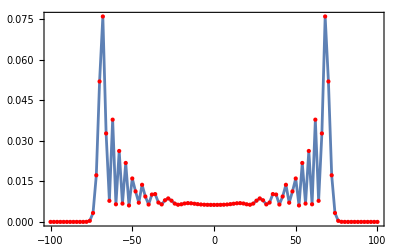

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
MeshStyle->Directive[PointSize[Medium],Red],
ImageSize->Full
]
```

## Alternative DTQW

```mathematica
state=VectorState[{{1/Sqrt[2.],0,0},{ⅈ/Sqrt[2.],1,0}}]
```

VectorState[{{0.707107,0,0},{0.+0.707107 ⅈ,1,0}}]

```mathematica
{time,phi}=DTQW2[state,10]//Chop//AbsoluteTiming;
```

```mathematica
Quantity[time,"Seconds"]
```

6.0953 s

```mathematica
phi//Dimensions
```

{402,1}

```mathematica
rho=MatrixPartialTrace[phi.phi†,1,{2,201}];
```

```mathematica
probs=Abs@Diagonal[rho];
```

```mathematica
Total@probs
```

1.

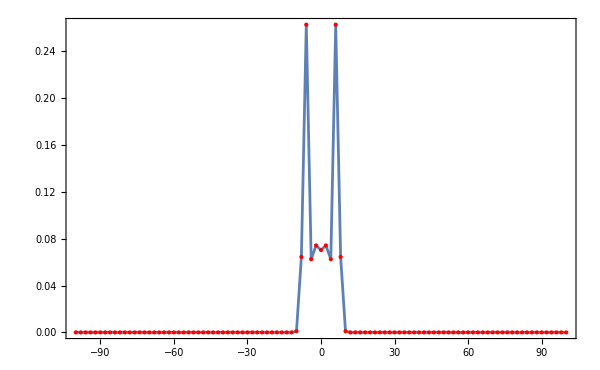

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
MeshStyle->Directive[PointSize[Medium],Red],
ImageSize->600
]
```

## DTQW testing (Density matrix state)

```mathematica
state=DMatrixState[{{1/2,0,0,0,0},{-ⅈ/2,0,0,1,0},{ⅈ/2,1,0,0,0},{1/2,1,0,1,0}}]
```

DMatrixState[{{1/2,0,0,0,0},{-ⅈ/2,0,0,1,0},{ⅈ/2,1,0,0,0},{1/2,1,0,1,0}}]

```mathematica
{time,rho}=DTQW[state,100]//Chop//AbsoluteTiming;
```

```mathematica
UnitConvert[#,"Minutes"]&@Quantity[time,"Seconds"]
```

2.06247 min

```mathematica
rrho=MatrixPartialTrace[rho,1,{2,201}];
```

```mathematica
probs=Abs@Diagonal[rrho];
```

```mathematica
Total@probs
```

1.

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
MeshStyle->Directive[PointSize[Medium],Red],
ImageSize->Full
]
```

-Graphics-

## Decoherence with StateVectors

```mathematica
state=VectorState[{{1/Sqrt[2.],0,0},{ⅈ/Sqrt[2.],1,0}}]
```

VectorState[{{0.707107,0,0},{0.+0.707107 ⅈ,1,0}}]

```mathematica
{time,rho}=DTQW2wDecoherence[state,0.99,100]//AbsoluteTiming;
```

```mathematica
Quantity[time,"Seconds"]
```

24.5581 s

```mathematica
positionrho=MatrixPartialTrace[rho,1,{2,201}];
```

```mathematica
probs=Abs@Diagonal[positionrho];
```

```mathematica
Total@probs
```

1.

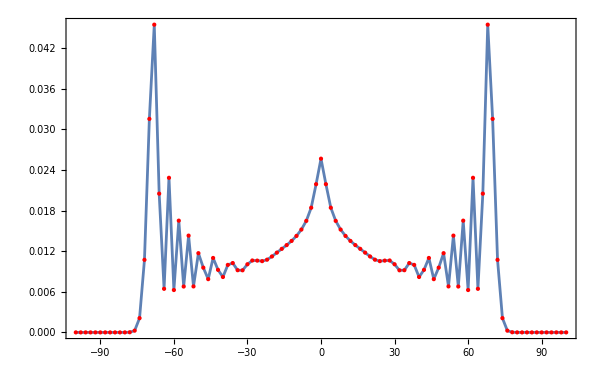

```mathematica
ListLinePlot[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
MeshStyle->Directive[PointSize[Medium],Red],
ImageSize->600
]
```

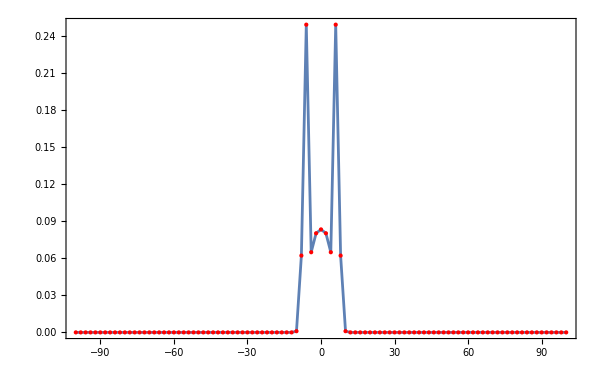
```mathematica
-Graphics--Graphics-
```